## Pregunta 1

```mathematica
a0 = 1/(p+d)Integrate[c,{t,-d,d}]
```

(2 c d)/(d+p)

```mathematica
an = 2/(p+d)Integrate[c Cos[(2 Pi n t)/(p+d)],{t,-d,d}]
```

(2 c Sin[(2 d n π)/(d+p)])/(n π)

```mathematica
Clear[a0,an]
```

```mathematica
(* Usemos de ejemplo con c= 8, d = 2, p =5 *)
```

```mathematica
c=8;d=2;p=5;
```

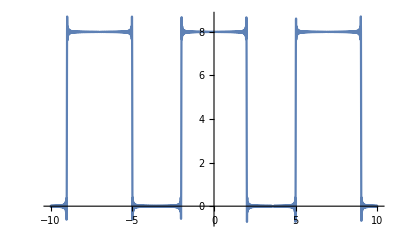

```mathematica
Plot[(2 c d)/(d+p)+(2 c)/Pi Sum[1/n Sin[(2 Pi n d)/(p+d)]Cos[(2Pi n t)/(p+d)],{n,1,200}],{t,-2p,2p},PlotRange->All]
```

```mathematica
Clear[c,d,p]
```

## Pregunta 2

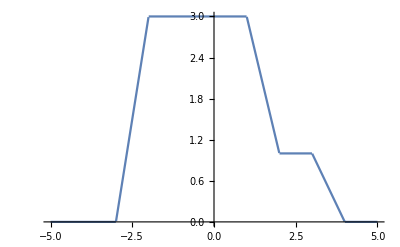

```mathematica
Plot[3(t+3)(UnitStep[t+3]-UnitStep[t+2])+3(UnitStep[t+2]-UnitStep[t-1])+(3-2(t-1))(UnitStep[t-1]-UnitStep[t-2])+
1(UnitStep[t-2]-UnitStep[t-3])+(1-(t-3))(UnitStep[t-3]-UnitStep[t-4]),{t,-5,5}]
```

```mathematica
FourierTransform[3(t+3)(UnitStep[t+3]-UnitStep[t+2])+3(UnitStep[t+2]-UnitStep[t-1])+(3-2(t-1))(UnitStep[t-1]-UnitStep[t-2])+
1(UnitStep[t-2]-UnitStep[t-3])+(1-(t-3))(UnitStep[t-3]-UnitStep[t-4]),t,w,FourierParameters->{1, -1}]
```

(2 ⅇ^(-ⅈ w))/w^2-(2 ⅇ^(-2 ⅈ w))/w^2+(3 ⅇ^(2 ⅈ w))/w^2+ⅇ^(-3 ⅈ w)/w^2-(3 ⅇ^(3 ⅈ w))/w^2-ⅇ^(-4 ⅈ w)/w^2

## Pregunta 3

```mathematica
(*Suponer poniendo el sin normal con la expansion de Fourier, vemos que son iguales, excepto cuando la senal esta en 0 como se debe.*)
```

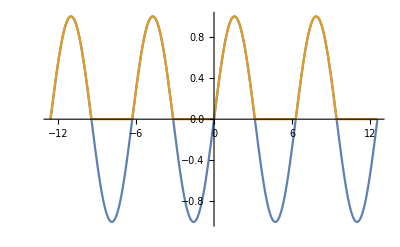

```mathematica
Plot[{Sin[t],1/Pi+Sum[(1+(-1)^n)/(Pi(1-n^2))Cos[n t],{n,2,100}]+1/2 Sin[t]},{t,-4Pi,4Pi}]
```

```mathematica
1/Pi^2+1/2(1/2^2+(2/(Pi(1-2^2)))^2)
```

1/2 (1/4+4/(9 π^2))+1/π^2

```mathematica
N[1/2 (1/4+4/(9 π^2))+1/π^2]
```

0.248837

## Pregunta 4

```mathematica
FourierTransform[2(Sin[2t]^2-Cos[t]^2),t,w,FourierParameters->{1, -1}]
```

-π DiracDelta[-4+w]-π DiracDelta[-2+w]-π DiracDelta[2+w]-π DiracDelta[4+w]

```mathematica
1/(2Pi)(  Integrate[(-π DiracDelta[-4+w]-π DiracDelta[-2+w]-π DiracDelta[2+w]-π DiracDelta[4+w])Exp[I w t],{w,-3,-1}] +
 Integrate[(-π DiracDelta[-4+w]-π DiracDelta[-2+w]-π DiracDelta[2+w]-π DiracDelta[4+w])Exp[I w t],{w,1,3}])
```

(-ⅇ^(-2 ⅈ t) π-ⅇ^(2 ⅈ t) π)/(2 π)

```mathematica
ExpToTrig[(-ⅇ^(-2 ⅈ t) π-ⅇ^(2 ⅈ t) π)/(2 π)]
```

-Cos[2 t]

### Pregunta 5

```mathematica
a0=1/Pi( Integrate[Pi^2(UnitStep[t+Pi]-UnitStep[t])+(t-Pi)^2(UnitStep[t]-UnitStep[t-Pi]),{t,-Pi,Pi}]  )
```

(4 π^2)/3

```mathematica
an = Simplify[1/Pi( Integrate[(Pi^2(UnitStep[t+Pi]-UnitStep[t])+(t-Pi)^2(UnitStep[t]-UnitStep[t-Pi]))Cos[n t],{t,-Pi,Pi}]  ),Element[n,Integers]]
```

2/n^2

```mathematica
bn = Simplify[1/Pi( Integrate[(Pi^2(UnitStep[t+Pi]-UnitStep[t])+(t-Pi)^2(UnitStep[t]-UnitStep[t-Pi]))Sin[n t],{t,-Pi,Pi}]  ),Element[n,Integers]]
```

(-2+(-1)^n (2+n^2 π^2))/(n^3 π)

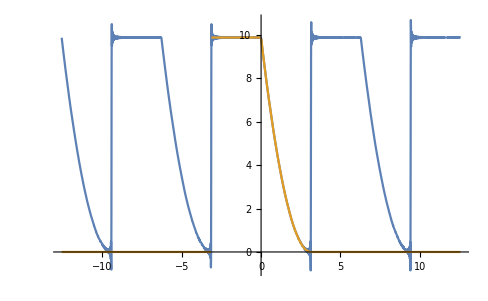

```mathematica
Plot[{(2 Pi^2)/3+Sum[(2 Cos[n t])/n^2+(-2+(-1)^n (2+n^2 π^2))/(n^3 π)Sin[n t],{n,1,200}],Pi^2(UnitStep[t+Pi]-UnitStep[t])+(t-Pi)^2(UnitStep[t]-UnitStep[t-Pi])},{t,-4Pi,4Pi}]
```

```mathematica
Sum[(-1)^(n+1)/n^2,{n,1,Infinity}]
```

π^2/12

## Pregunta 6

### (6.a)

```mathematica
Simplify[FourierTransform[t^2 Exp[-5 Abs[t]],t,w,FourierParameters->{1, -1}]]
```

(500-60 w^2)/((25+w^2)^3)

```mathematica
Simplify[2/(5-I w)^3+2/(5+I w)^3]
```

(500-60 w^2)/((25+w^2)^3)

```mathematica
(*Dan lo mismo*)
```

```mathematica
FourierTransform[t^2 Exp[-5 t] UnitStep[t],t,w,FourierParameters->{1, -1}]
```

(2 ⅈ)/(-5 ⅈ+w)^3

```mathematica
FourierTransform[t^2 Exp[5 t] UnitStep[-t],t,w,FourierParameters->{1, -1}]
```

-(2 ⅈ)/(5 ⅈ+w)^3

```mathematica
Expand[(w I  +4)^2-7]
```

9+8 ⅈ w-w^2

### (6.b)

```mathematica
InverseFourierTransform[(10(4+I w))/(9-w^2+8 I w),w,t,FourierParameters->{1, -1}]
```

5 ⅇ^(-(4+√7) t) (1+ⅇ^(2 √7 t)) HeavisideTheta[t]

```mathematica
InverseFourierTransform[(-10I w)/(w^2-7),w,t,FourierParameters->{1, -1}]
```

5/2 ⅇ^(-ⅈ √7 t) (1+ⅇ^(2 ⅈ √7 t)) Sign[t]